```mathematica
Clear["Global`*"];
Clear["Local`*"];
Unprotect[In,Out];
Clear[In,Out];
Protect[In, Out];
MemoryInUse[];
CloseKernels[];
LaunchKernels[6];
```

Bins the simulation data, not needed unless new data is available

```mathematica
(*loca="/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/model_driven_theory/2018/data";
opt="2";
mingB={0.05,0.1,0.2,0.25,0.5,0.75,1};
gMax={1.,2.,3.,4.,5.,6.,7.,8.,9.,10.};
(*gMax={1,2,3,4,5,6,7,8,9,10};*)
gMax={10,10,10,10,10,10,10,10,10,10};
mn1=5;
geneList=Range[mingB[[mn1]],gMax[[#]],mingB[[mn1]]]&/@Range[1,Length[gMax]]
geneN=Length/@geneList
order=cycles=(ToString/@#)&/@{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}};
rn=10;num=1;
ploidy={"1","2","3"};
p=1;
ge2Ldt=ReadList[loca<>"/"<>"cycletheory2018-G1E-"<>ploidy[[p]]<>"n-singleCellCount-prob"<>opt<>"-rpinf-"<>ToString[geneN[[num]]]<>"-"<>ToString[gMax[[num]]]<>"-1-1-"<>StringJoin[Take[order[[#]],1]]<>".dat"][[All,2;;geneN[[num]]+1]]&/@{1,5,10};
pp=Map[Function[dum,
geneLength=geneList[[1]];
(*Range[mingB[[mn1]],gMax[[#]],mingB[[mn1]]]&/@Range[1,Length[gMax]]*)
(*geneLength={1,2,3};*)
geneBine={0,gMax[[dum]]/3+0.05,2*gMax[[dum]]/3+0.05,gMax[[dum]]+0.05};
Print[geneBine];
cc=Partition[geneBine,2,1]//N;
shift=0;
col1=Table[Flatten[Position[geneLength,#]&/@Select[geneLength, #>=cc[[i,1]] && #<cc[[i,2]]&]]+shift,{i,1,Length[cc]}];
(*Table[If[col1[[i]]≠ {},
ge2Ldt[[dum]][[Range[Min[col1[[i]]],Max[col1[[i]]]]]]/. 0 ->Null,{Null}],{i,1,Length[col1]}]]*)
tp=Table[If[col1[[i]]≠ {},
Mean/@ge2Ldt[[dum]][[All,Range[Min[col1[[i]]],Max[col1[[i]]]]]],{0}],{i,1,Length[col1]}];
Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/SourceFiles/data/Figure2_data_sims-"<>ToString[dum]<>".dat",N[tp]];
tp]
(*(Flatten[Table[Mean[Select[#[[Min[col1[[i]]];;Max[col1[[i]]]]],#>0&]/.{}->{0}],{i,1,Length[col1]}]]&/@ge2Ldt[[dum]])]*),
Range[1,Length[ge2Ldt]]
];*)
```

{{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.},{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.},{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.},{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.},{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.},{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.},{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.},{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.},{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.},{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.}}

{20,20,20,20,20,20,20,20,20,20}

{0,3.38333,6.71667,10.05}

{0,3.38333,6.71667,10.05}

{0,3.38333,6.71667,10.05}

Import simulation data already binned

```mathematica
loca="/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/SourceFiles/data/sim_data";
pp=Import[loca<>"/Bins_data_sims-1010"<>ToString[#]<>".dat","Data"]&/@Range[1,3];
```

Plot simulation data

1

{0,3.38333,6.71667,10.05}

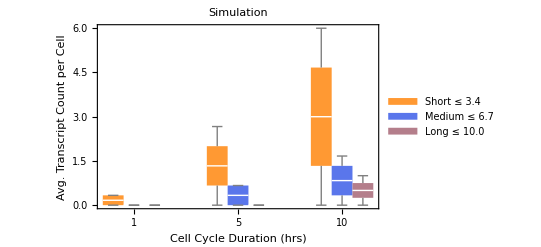

```mathematica
genomeLength=If[#[[1]]==0,Range[#[[2]],#[[3]],#[[4]]],#[[2]]]&/@{{0,1,10,1},{0,0.1,1,0.1},{0,0.5,3,0.5},{0,0.05,3,0.05}(*,0.005,0.0005*)(*,5,3*)};
gl=1
geneBine={0,Max[genomeLength[[gl]]]/3+0.05,2*Max[genomeLength[[gl]]]/3+0.05,Max[genomeLength[[gl]]]+0.05};
Print[geneBine];

ap=BoxWhiskerChart[N[pp],ChartStyle->{Lighter[Orange,0.20],
(*Lighter[Purple,0.5],
Lighter[Yellow,0.75],*)
(*Lighter[Blue,0.05],*)
ColorData["ThermometerColors"][0.15],ColorData[24][8]},BarSpacing->{0,2,4},ChartLabels->{(*"Cell Cycle Duration",*){"1","5","10"},{None,None,None}},ChartLegends->{"Short ≤ "<>ToString[NumberForm[geneBine[[2]],{2,1}]],"Medium ≤ "<>ToString[NumberForm[geneBine[[3]],{2,1}]],"Long ≤ "<>ToString[NumberForm[geneBine[[4]],{2,1}]]},FrameStyle->Black,FrameLabel->{"Cell Cycle Duration (hrs)","Avg. Transcript Count per Cell"},PlotLabel->Style["Simulation",Black],BaseStyle->{18,Black,"Helvetica"},ImageSize->400]
(*BoxWhiskerChart[mx0,"Outliers",ChartStyle->{Lighter[Orange,0.20],
(*Lighter[Purple,0.5],
Lighter[Yellow,0.75],*)
(*Lighter[Blue,0.05],*)
ColorData["ThermometerColors"][0.15],ColorData[24][8]},BarSpacing->{0,1,2}]*)
```

Import xenopus tropicalis data already binned

```mathematica
loca="/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/SourceFiles/data/binned_shorttolong";
(*(*0,5000,50000,5000000}*)
mkx=Import[loca<>"/"<>#<>"-2.dat","Data"]&/@{"10hpf","14hpf","18hpf"};*)

(*0,10000,250000,5000000}*)
mkxa=Import[loca<>"/"<>#<>"-2a.dat","Data"]&/@{"10hpf","14hpf","18hpf"};
```

Plot Xenopus Data

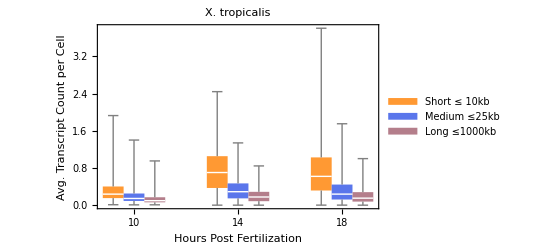

```mathematica
(*bpX1=BoxWhiskerChart[mkx,ChartStyle->{Lighter[Orange,0.20],
(*Lighter[Purple,0.5],
Lighter[Yellow,0.75],*)
(*Lighter[Blue,0.05],*)
ColorData["ThermometerColors"][0.15],ColorData[24][8]},BarSpacing->{0,2,4},ChartLabels->{(*"Cell Cycle Duration",*){"10",(*"11",*)(*"12",*)(*"13",*)"14",(*"16",*)"18"(*,"20","22"*)},{None,None,None}},ChartLegends->{"Short ≤ 5kb","Medium ≤50kb","Long ≤1000kb"},(*FrameLabel->{"Cell Cycle Duration (hrs)","Avg. Transcript Count per Cell"},*)FrameLabel->{"Hours Post Fertilization","Avg. Transcript Count per Cell"},FrameStyle->Black,PlotLabel->Style["X. tropicalis",Italic,Black],BaseStyle->{18,Black,"Helvetica"},ImageSize->400]*)
bpX2=BoxWhiskerChart[mkxa,ChartStyle->{Lighter[Orange,0.20],
(*Lighter[Purple,0.5],
Lighter[Yellow,0.75],*)
(*Lighter[Blue,0.05],*)
ColorData["ThermometerColors"][0.15],ColorData[24][8]},BarSpacing->{0,2,4},ChartLabels->{(*"Cell Cycle Duration",*){"10",(*"11",*)(*"12",*)(*"13",*)"14",(*"16",*)"18"(*,"20","22"*)},{None,None,None}},ChartLegends->{"Short ≤ 10kb","Medium ≤25kb","Long ≤1000kb"},(*FrameLabel->{"Cell Cycle Duration (hrs)","Avg. Transcript Count per Cell"},*)FrameLabel->{"Hours Post Fertilization","Avg. Transcript Count per Cell"},FrameStyle->Black,PlotLabel->Style["X. tropicalis",Italic,Black],BaseStyle->{18,Black,"Helvetica"},ImageSize->400]
```

```mathematica
tad=TableForm[{{Panel[ap,Style["A",30,Black,Bold],Appearance->"Frameless",Background->White],Panel[bpX2,Style["B",30,Black,Bold],Appearance->"Frameless",Background->White]}},TableSpacing->{Automatic,5}]
```

-Graphics-A | -Graphics-B

```mathematica
Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/2-Figure2-whisker.pdf",tad]
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/2-Figure2-whisker.pdf